Probability of l<b without branch

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability of b<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)^2
```

Probability of l=L

```mathematica
P3[L_,p_]:=p^L*(1-p)
```

Probability of b<=l<L with branch

```mathematica
P4[l_,p_]:=p^(l+1)*(1-p)
```

Probability of b=L with branch

```mathematica
P5[L_,p_]:=p^(L+1)
```

```mathematica
S1[L_,b_,p_]:=Sum[P1[l,p]*Log[((L-b)*2+b),P1[l,p]],{l,0,b-1}]
S2[L_,b_,p_]:=Sum[P2[l,p]*Log[((L-b)*2+b),P2[l,p]],{l,b,L-1}]
S3[L_,b_,p_]:=Sum[P4[l,p]*Log[((L-b)*2+b),P4[l,p]],{l,b,L-1}]
Em[L_,b_,p_]:=-(S1[L,b,p]+S2[L,b,p]+S3[L,b,p]+P3[L,p]*Log[((L-b)*2+b),P3[L,p]]+P5[L,p]*Log[((L-b)*2+b),P5[L,p]])
```

```mathematica
S4[L_,p_]:=Sum[P1[l,p]*Log[(L+1),P1[l,p]],{l,0,L-1}]
```

```mathematica
Em2[L_,p_]:=-(S4[L,p]+p^L*Log[(L+1),p^L])
```

This is my equation for entropy that I calculated using geometric and arithmetic sums. I does not match the above

```mathematica
En[L_,b_,p_]:=(1-p)(Log[1-p]*(1-p^b)/(1-p)+Log[p]*((b-1)p^b/(1-p)+p(1-p^(b-1))/(1-p)^2))+(1-p)^2(p^b(1-p^(L-b))/(1-p)Log[(1-p)^2] +Log[p]((L-1)*p^L/(1-p)+p(1-p^(L-1))/(1-p)^2-(b-1)p^b/(1-p)-p(1-p^(b-1))/(1-p)^2))+(1-p)*(Log[1-p]*p^(b+1)(1-p^(L-b))/(1-p)+Log[p]+p(1-p^L)/(1-p)^2+L*p^(L+1)/(1-p)-p(1-p^b)/(1-p)^2+b*p^(L+1)/(1-p))+p^L*(1-p)Log[p^L*(1-p)]+p^(L+1)*Log[p^(L+1)]
```

Adjusted rates

```mathematica
h[τ_]:=1/(1+1/τ)
```

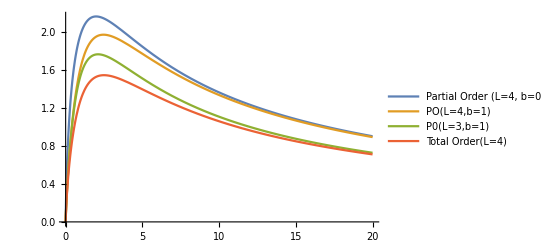

```mathematica
Plot[{Em[4,0,h[τ]],Em[4,1,h[τ]],Em[3,1,h[τ]],Em2[4,h[τ]]},{τ,0,20},PlotLegends->{"Partial Order (L=4, b=0)","PO(L=4,b=1)","P0(L=3,b=1)","Total Order(L=4)"}]
```

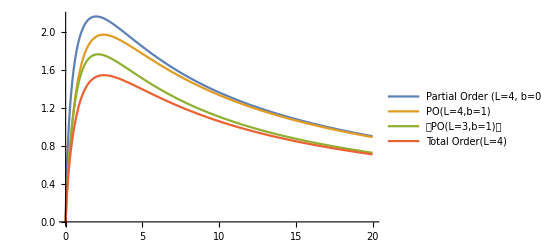

```mathematica
T1=Evaluate@Table[Em[4,b,h[τ]],{b,0,3}];
```

```mathematica
T2=Evaluate@Table[Em[3,b,h[τ]],{b,0,2}];
```

```mathematica
T3=Evaluate@Table[Em[2,b,h[τ]],{b,0,1}];
```

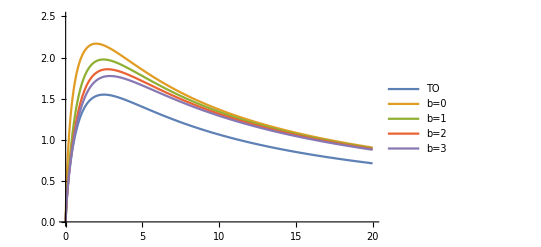

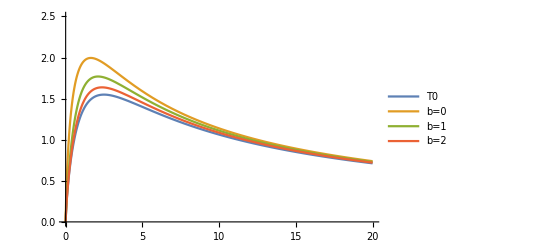

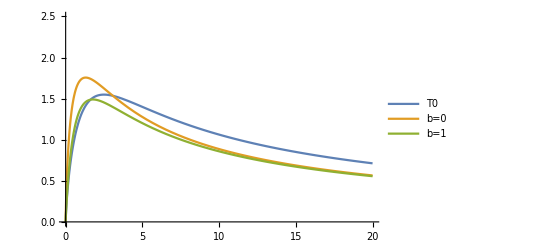

```mathematica
Plot[{Em2[4,h[τ]],T1},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"TO","b=0","b=1","b=2","b=3"}]
Plot[{Em2[4,h[τ]],T2},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"T0","b=0","b=1","b=2"}]
Plot[{Em2[4,h[τ]],T3},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"T0","b=0","b=1"}]
```

```mathematica
Ln=4;
Br=2;
```

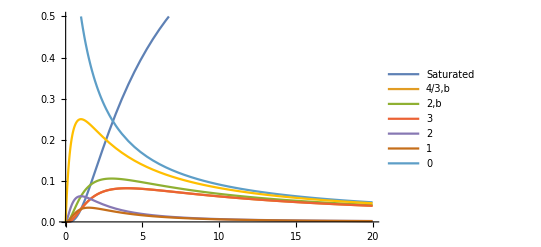

```mathematica
T4=Evaluate@Table[P1[l,h[τ]],{l,0,Br-1}];
T5=Evaluate@Table[P2[l,h[τ]],{l,Br,Ln-1}];
T6=Evaluate@Table[P4[l,h[τ]],{l,Br,Ln-1}];
Plot[{P5[Ln,h[τ]],P3[Ln,h[τ]],T6,T5,T4},{τ,0,20},PlotRange->{0,0.5},PlotLegends->{"Saturated","4/3,b","2,b","3","2","1","0"}]
```

```mathematica
Table[P4[l,h[τ]],{l,2,3}]
```

```mathematica
NT4=Length[T4];
NT5=Length[T5];
NT6=Length[T6];
```

{{1/(1+1/τ)^5+(1-1/(1+1/τ))/(1+1/τ)^4+(1-1/(1+1/τ))/(1+1/τ)^3+(1-1/(1+1/τ))^2/(1+1/τ)^2},{1/(1+1/τ)^5+(1-1/(1+1/τ))/(1+1/τ)^4+(1-1/(1+1/τ))/(1+1/τ)^3+(1-1/(1+1/τ))^2/(1+1/τ)^3+(1-1/(1+1/τ))^2/(1+1/τ)^2}}

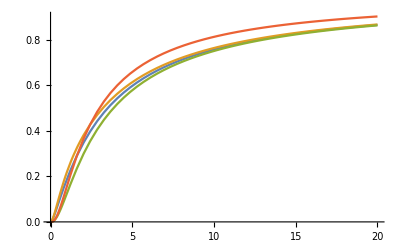

```mathematica
CU1[L_,p_]:=P5[L,p]+P3[L,p];
T62=Evaluate@Table[CU1[Ln,h[τ]]+Sum[T6[[{i}]],{i,1,j}],{j,1,NT6}];
T52=Evaluate@Table[T62[[NT6-1]]+Sum[T5[[{i}]],{i,1,j}],{j,1,NT4}];
T42=Evaluate@Table[T52[[NT5-1]]+Sum[T4[[{i}]],{i,1,j}],{j,1,NT5}];

T52
Plot[{P5[Ln,h[τ]],CU1[Ln,h[\tau},{τ,0,20}]
```